```mathematica
(*{q,a,p},{q,b,r},{p,a,r}*)

(*A=(S,f,S.)*)
(*S: conj finito de estados*)
(*f: Sn+1->S  función de transición local de A*)
(*S.: lista de estados incluida en S*)


(*EJERCICIO 1*)
(*Implemente un módulo en Mathematica que, tomando como entrada un AFD proporcione como salida un AC unidireccional unidimensional que acepte el mismo lenguaje que el AFD mediante entrada paralela.*)
Ejercicio1[automata_]:=Module[{estados,alfabeto,trans,regla,i,j},
estados = automata[[1]];  (*Q,P,R*)
alfabeto=automata[[2]]; (*a,b*)
trans=automata[[3]];
regla={};
(*crear una regla por cada estado posible*)
For[i=1,i≤Length[estados],i++,
For [j=1,j≤Length[estados],j++,
AppendTo[regla,{estados[[i]],estados[[j]],estados[[j]]}];
];
];
(*una regla por cada símbolo*)
For[i=1,i≤Length[alfabeto],i++,
For [j=1,j≤Length[alfabeto],j++,
AppendTo[regla,{alfabeto[[i]],alfabeto[[j]],alfabeto[[j]]}];
];
];
(*una regla por cada transición*)
For [i=1,i≤Length[trans],i++,
AppendTo[regla,trans[[i]]];
];
Return[{estados,Union[regla],automata[[5]]}];
];
cel1=Ejercicio1[{{Q,P,R},{a,b},{{Q,a,P},{Q,b,R},{P,a,R},{P,b,Q},{R,a,R},{R,b,R}},{Q},{R}}]
```

{{Q,P,R},{{a,a,a},{a,b,b},{b,a,a},{b,b,b},{P,a,R},{P,b,Q},{P,P,P},{P,Q,Q},{P,R,R},{Q,a,P},{Q,b,R},{Q,P,P},{Q,Q,Q},{Q,R,R},{R,a,R},{R,b,R},{R,P,P},{R,Q,Q},{R,R,R}},{R}}

```mathematica
(*EJERCICIO 2*)
(*Implemente un módulo Mathematica que, tomando como entrada una cadena arbitraria,un AC que reconoce un lenguaje mediante entrada paralela en tiempo real y un estado de frontera q S,proporcione como salida True si el AC acepta la cadena y False en caso contrario.*)

Ejercicio2 [cadena_, celula_, q_]:=Module[{i,reglas,estadosF,pal},
reglas = celula[[2]];  
estadosF=celula[[3]]; 
(*poner el estado frontera como prefijo de la cadena*)
pal = Prepend[cadena,q];
(*recorrer la cadena*)
For [i=1,i≤Length[cadena],i++,
pal = Siguiente[pal,reglas];
];
Return[MemberQ[estadosF,pal[[Length[cadena]+1]]]];
(*comprobar si símbolo salida pertenece a estados finales ac: Pertenece al lenguaje*)
];
```

```mathematica
Siguiente[pal_,reglas_]:=Module[{salida,j,aux,sol},
salida={}; (*el nuevo estado*)
(*Calcular el resultado de cada celda teniendo en cuenta a la vecina de la izquierda*) 
For[j=2,j≤Length[pal],j++, (*la primera celda no se tiene en cuenta por ser la barrera q*)
aux={pal[[j-1]],pal[[j]],_};
sol=Cases[reglas,aux];    
AppendTo[salida, sol[[1,3]]]; (*añadir a la palabra el nuevo estado*)
];
salida = Prepend[salida,pal[[1]]];
Return[salida];
];
```

```mathematica
Ejercicio2[{a,b,a,a,b},cel1,Q]
```

True

```mathematica
(*EJERCICIO 3*)
(*Implemente un módulo Mathematica que muestre la secuencia de computación que se lleva a cabo en el módulo propuesto en la actividad (2) mediante un diagrama espaciotemporal.(Nota:Utilice las funciones ArrayPlot y ListAnimate explicados en la práctica de Fundamentos Básicos)*)
```

```mathematica
Ejercicio3[cadena_,celula_,q_]:=Module[{reglas, estadosF,pal,out,i,salida,sol,colores,coloresF,aux},
reglas = celula[[2]];  
estadosF=celula[[3]];
(*poner el estado frontera como prefijo de la cadena*)
pal = Prepend[cadena,q];
out={};(*lo que se va a mostrar por pantalla. La frontera q no hace falta*)
PrependTo[out,cadena];
(*recorrer la cadena*)
For [i=1,i≤Length[cadena],i++,
pal = Siguiente[pal,reglas];
PrependTo[out,Rest[pal]];
]; (*Fin for i*)
(*generar tantos colores como símbolos diferentes existan, para la representación gráfica*)
aux = Flatten[reglas];
aux = Union[aux];(*quita los duplicados*)
colores = GeneradorC[Length[aux]];
coloresF={};
(*asignar un color a cada símbolo*)
For [i=1,i≤Length[aux],i++,
AppendTo[coloresF,aux[[i]]->colores[[i]]];
];
Return[{ArrayPlot[out,ColorRules->coloresF],coloresF}];


];
```

```mathematica
GeneradorC[cad_]:=Module[{res,i,j,k,suma},
res = {};
suma = 1/Floor[CubeRoot[cad-1]]; (*para que los colores varíen en función de la longitud*)
For[i=0,i≤1≤cad,i=i+suma,
For [j=0,j≤1≤cad,j=j+suma,
For[k=0,k≤1≤cad,k=k+suma,
AppendTo[res,{RGBColor[i,j,k]}];
];
];
];
Return[RandomSample[res]]
];
```

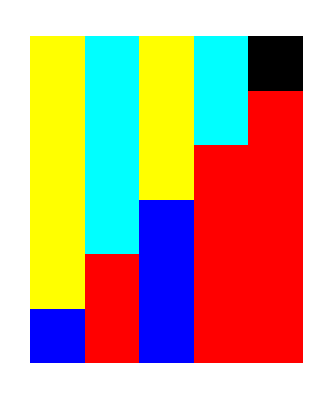
{-Graphics-,{a→{RGBColor[0, 0, 1]},b→{RGBColor[1, 0, 0]},P→{RGBColor[1, 1, 0]},Q→{RGBColor[0, 1, 1]},R→{RGBColor[0, 0, 0]}}}

```mathematica
Ejercicio3[{a,b,a,b,b},cel1,Q]
```